# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

## Setup

### Parameters

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

```mathematica
rtMax=1.8;
```

```mathematica
rtMin=0.6;
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01","2022-12-01","2023-01-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2.3.20,BA.2.75,BA.2.75.2,BA.2.75.4,BA.4.6,BA.5,BA.5.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.22,BA.5.1.27,BA.5.1.5,BA.5.2,BA.5.2.1,BA.5.2.13,BA.5.2.20,BA.5.2.21,BA.5.2.23,BA.5.2.34,BA.5.2.35,BA.5.2.6,BA.5.2.9,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.6,BE.1,BE.1.1,BE.1.1.1,BE.1.2.1,BE.1.4.2,BE.4.2,BF.10,BF.11,BF.13,BF.14,BF.26,BF.32,BF.5,BF.7,BF.7.4,BF.7.4.1,BF.7.5,BN.1,BN.1.2,BN.1.3,BN.1.3.1,BN.1.4,BN.1.5,BQ.1,BQ.1.1,BQ.1.10,BQ.1.10.1,BQ.1.1.1,BQ.1.11,BQ.1.1.10,BQ.1.1.13,BQ.1.1.18,BQ.1.1.2,BQ.1.12,BQ.1.1.28,BQ.1.1.3,BQ.1.13,BQ.1.1.4,BQ.1.14,BQ.1.1.5,BQ.1.15,BQ.1.1.6,BQ.1.1.7,BQ.1.18,BQ.1.2,BQ.1.22,BQ.1.23,BQ.1.25,BQ.1.3,BQ.1.5,BQ.1.6,BQ.1.8,BU.1,BW.1.1,CH.1.1,CK.1,CK.2.1.1,CM.8.1,CN.1,CP.1,CQ.2,CR.1.1,DF.1,other,XBB,XBB.1,XBB.1.5,XBB.2,XBB.3}

```mathematica
n=Length[variants]
```

96

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

61

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

35

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

96

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv"],1]];
```

```mathematica
clades={"other","21L (Omicron)","22A (Omicron)","22B (Omicron)","22C (Omicron)","22D (Omicron)","22E (Omicron)","22F (Omicron)"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.54357188, 0.73433536, 0.41441192],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L (Omicron)→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A (Omicron)→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],22B (Omicron)→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],22C (Omicron)→RGBColor[0.54357188, 0.73433536, 0.41441192],22D (Omicron)→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],22E (Omicron)→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2.3.20→RGBColor[0.1715652, 0.057908600000000005, 0.31848920000000003],CM.8.1→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.4.6→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],BA.5→RGBColor[0.1788741855319149, 0.3281657804255319, 0.3386725855319149],BA.5.1→RGBColor[0.18632727659574466, 0.34183935460992904, 0.3527839432624114],BA.5.1.10→RGBColor[0.19378036765957446, 0.3555129287943262, 0.36689530099290785],BA.5.1.18→RGBColor[0.20123345872340426, 0.36918650297872335, 0.3810066587234043],BA.5.1.22→RGBColor[0.20868654978723405, 0.38286007716312054, 0.39511801645390077],BA.5.1.27→RGBColor[0.21613964085106382, 0.3965336513475177, 0.4092293741843972],BA.5.1.5→RGBColor[0.2235927319148936, 0.41020722553191485, 0.42334073191489363],BA.5.2→RGBColor[0.2310458229787234, 0.42388079971631204, 0.4374520896453902],BA.5.2.1→RGBColor[0.2384989140425532, 0.43755437390070917, 0.4515634473758866],BA.5.2.20→RGBColor[0.245952005106383, 0.45122794808510636, 0.46567480510638304],BA.5.2.21→RGBColor[0.2534050961702128, 0.46490152226950354, 0.47978616283687947],BA.5.2.23→RGBColor[0.2608581872340425, 0.47857509645390073, 0.49389752056737596],BA.5.2.34→RGBColor[0.2683112782978723, 0.4922486706382978, 0.5080088782978724],BA.5.2.6→RGBColor[0.2757643693617021, 0.505922244822695, 0.5221202360283689],BA.5.2.9→RGBColor[0.2832174604255319, 0.5195958190070922, 0.5362315937588653],BA.5.3.1→RGBColor[0.2906705514893617, 0.5332693931914894, 0.5503429514893617],BA.5.5→RGBColor[0.29812364255319146, 0.5469429673758865, 0.5644543092198582],BA.5.5.1→RGBColor[0.30557673361702126, 0.5606165415602836, 0.5785656669503547],BA.5.6→RGBColor[0.31302982468085105, 0.5742901157446808, 0.5926770246808511],BE.1→RGBColor[0.32048291574468085, 0.587963689929078, 0.6067883824113476],BE.1.1→RGBColor[0.32793600680851065, 0.6016372641134752, 0.620899740141844],BF.10→RGBColor[0.3353890978723404, 0.6153108382978723, 0.6350110978723406],BF.11→RGBColor[0.3428421889361702, 0.6289844124822694, 0.649122455602837],BF.13→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],BF.26→RGBColor[0.36411878468085107, 0.6502610082269503, 0.6703990513475179],BF.5→RGBColor[0.3779422893617021, 0.657864029787234, 0.6775642893617022],BF.7→RGBColor[0.3917657940425532, 0.6654670513475177, 0.6847295273758867],BF.7.4→RGBColor[0.4055892987234042, 0.6730700729078014, 0.691894765390071],BF.7.4.1→RGBColor[0.4194128034042553, 0.6806730944680851, 0.6990600034042554],CK.1→RGBColor[0.4332363080851064, 0.6882761160283688, 0.7062252414184398],CQ.2→RGBColor[0.4470598127659574, 0.6958791375886524, 0.7133904794326242],BA.5.1.12→RGBColor[0.4608833174468085, 0.7034821591489362, 0.7205557174468086],BA.5.2.13→RGBColor[0.4747068221276596, 0.7110851807092198, 0.727720955460993],BA.5.2.35→RGBColor[0.4885303268085106, 0.7186882022695035, 0.7348861934751774],BE.1.1.1→RGBColor[0.5023538314893616, 0.7262912238297872, 0.7420514314893618],BE.1.2.1→RGBColor[0.5161773361702128, 0.7338942453900709, 0.7492166695035462],BE.1.4.2→RGBColor[0.5300008408510638, 0.7414972669503546, 0.7563819075177306],BE.4.2→RGBColor[0.5438243455319149, 0.7491002885106383, 0.7635471455319149],BF.14→RGBColor[0.557647850212766, 0.756703310070922, 0.7707123835460994],BF.32→RGBColor[0.571471354893617, 0.7643063316312056, 0.7778776215602837],BF.7.5→RGBColor[0.585294859574468, 0.7719093531914893, 0.7850428595744682],BU.1→RGBColor[0.5991183642553192, 0.779512374751773, 0.7922080975886525],CK.2.1.1→RGBColor[0.6129418689361702, 0.7871153963120567, 0.799373335602837],CN.1→RGBColor[0.6267653736170213, 0.7947184178723404, 0.8065385736170213],CP.1→RGBColor[0.6405888782978724, 0.8023214394326241, 0.8137038116312058],CR.1.1→RGBColor[0.6544123829787234, 0.8099244609929078, 0.8208690496453901],DF.1→RGBColor[0.6682358876595744, 0.8175274825531915, 0.8280342876595745],BA.2.75→RGBColor[0.38951687999999995, 0.36243652666666665, 0.13373712666666668],BN.1→RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],BN.1.3→RGBColor[0.5453236319999999, 0.5074111373333333, 0.18723197733333335],CH.1.1→RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],BA.2.75.2→RGBColor[0.7011303839999999, 0.6523857479999999, 0.240726828],BA.2.75.4→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],BN.1.2→RGBColor[0.8011303839999999, 0.752385748, 0.34072682800000004],BN.1.3.1→RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],BN.1.4→RGBColor[0.8453236319999999, 0.8074111373333333, 0.48723197733333334],BN.1.5→RGBColor[0.867420256, 0.834923832, 0.560484552],BQ.1→RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],BQ.1.1→RGBColor[0.48301446428571426, 0.2892171428571429, 0.11162464285714287],BQ.1.10→RGBColor[0.5152154285714285, 0.30849828571428584, 0.11906628571428574],BQ.1.10.1→RGBColor[0.5474163928571428, 0.32777942857142867, 0.1265079285714286],BQ.1.11→RGBColor[0.5796173571428571, 0.3470605714285715, 0.13394957142857145],BQ.1.1.13→RGBColor[0.6118183214285714, 0.3663417142857144, 0.1413912142857143],BQ.1.1.18→RGBColor[0.6440192857142857, 0.38562285714285727, 0.14883285714285716],BQ.1.12→RGBColor[0.67622025, 0.4049040000000001, 0.1562745],BQ.1.1.3→RGBColor[0.7084212142857143, 0.424185142857143, 0.16371614285714287],BQ.1.13→RGBColor[0.7406221785714285, 0.4434662857142858, 0.17115778571428575],BQ.1.1.4→RGBColor[0.7728231428571428, 0.4627474285714287, 0.1785994285714286],BQ.1.14→RGBColor[0.8050241071428571, 0.48202857142857153, 0.18604107142857146],BQ.1.1.5→RGBColor[0.8372250714285714, 0.5013097142857144, 0.1934827142857143],BQ.1.2→RGBColor[0.8694260357142857, 0.5205908571428572, 0.20092435714285717],BQ.1.22→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],BQ.1.23→RGBColor[0.9051403214285714, 0.5563051428571429, 0.23663864285714287],BQ.1.25→RGBColor[0.9086536428571428, 0.5727382857142859, 0.26491128571428574],BQ.1.3→RGBColor[0.9121669642857142, 0.5891714285714287, 0.2931839285714286],BQ.1.5→RGBColor[0.9156802857142857, 0.6056045714285715, 0.3214565714285714],BQ.1.1.1→RGBColor[0.9191936071428571, 0.6220377142857144, 0.3497292142857143],BQ.1.1.10→RGBColor[0.9227069285714286, 0.6384708571428572, 0.37800185714285717],BQ.1.1.2→RGBColor[0.92622025, 0.6549040000000002, 0.4062745],BQ.1.15→RGBColor[0.9297335714285714, 0.671337142857143, 0.43454714285714285],BQ.1.1.6→RGBColor[0.9332468928571428, 0.6877702857142858, 0.4628197857142857],BQ.1.1.7→RGBColor[0.9367602142857142, 0.7042034285714287, 0.49109242857142854],BQ.1.18→RGBColor[0.9402735357142857, 0.7206365714285715, 0.5193650714285715],BQ.1.6→RGBColor[0.9437868571428571, 0.7370697142857143, 0.5476377142857143],BQ.1.8→RGBColor[0.9473001785714286, 0.7535028571428573, 0.5759103571428572],XBB→RGBColor[0.516407208, 0.09422539200000002, 0.081998688],XBB.1→RGBColor[0.688542944, 0.12563385600000004, 0.10933158400000001],XBB.1.5→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],XBB.2→RGBColor[0.888542944, 0.32563385600000005, 0.30933158400000005],XBB.3→RGBColor[0.916407208, 0.49422539200000004, 0.481998688]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.1715652, 0.057908600000000005, 0.31848920000000003],RGBColor[0.38951687999999995, 0.36243652666666665, 0.13373712666666668],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.1788741855319149, 0.3281657804255319, 0.3386725855319149],RGBColor[0.18632727659574466, 0.34183935460992904, 0.3527839432624114],RGBColor[0.19378036765957446, 0.3555129287943262, 0.36689530099290785],RGBColor[0.20123345872340426, 0.36918650297872335, 0.3810066587234043],RGBColor[0.20868654978723405, 0.38286007716312054, 0.39511801645390077],RGBColor[0.21613964085106382, 0.3965336513475177, 0.4092293741843972],RGBColor[0.2235927319148936, 0.41020722553191485, 0.42334073191489363],RGBColor[0.2310458229787234, 0.42388079971631204, 0.4374520896453902],RGBColor[0.2384989140425532, 0.43755437390070917, 0.4515634473758866],RGBColor[0.245952005106383, 0.45122794808510636, 0.46567480510638304],RGBColor[0.2534050961702128, 0.46490152226950354, 0.47978616283687947],RGBColor[0.2608581872340425, 0.47857509645390073, 0.49389752056737596],RGBColor[0.2683112782978723, 0.4922486706382978, 0.5080088782978724],RGBColor[0.2757643693617021, 0.505922244822695, 0.5221202360283689],RGBColor[0.2832174604255319, 0.5195958190070922, 0.5362315937588653],RGBColor[0.2906705514893617, 0.5332693931914894, 0.5503429514893617],RGBColor[0.29812364255319146, 0.5469429673758865, 0.5644543092198582],RGBColor[0.30557673361702126, 0.5606165415602836, 0.5785656669503547],RGBColor[0.31302982468085105, 0.5742901157446808, 0.5926770246808511],RGBColor[0.32048291574468085, 0.587963689929078, 0.6067883824113476],RGBColor[0.32793600680851065, 0.6016372641134752, 0.620899740141844],RGBColor[0.3353890978723404, 0.6153108382978723, 0.6350110978723406],RGBColor[0.3428421889361702, 0.6289844124822694, 0.649122455602837],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.36411878468085107, 0.6502610082269503, 0.6703990513475179],RGBColor[0.3779422893617021, 0.657864029787234, 0.6775642893617022],RGBColor[0.3917657940425532, 0.6654670513475177, 0.6847295273758867],RGBColor[0.4055892987234042, 0.6730700729078014, 0.691894765390071],RGBColor[0.4194128034042553, 0.6806730944680851, 0.6990600034042554],RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],RGBColor[0.5453236319999999, 0.5074111373333333, 0.18723197733333335],RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],RGBColor[0.48301446428571426, 0.2892171428571429, 0.11162464285714287],RGBColor[0.5152154285714285, 0.30849828571428584, 0.11906628571428574],RGBColor[0.5474163928571428, 0.32777942857142867, 0.1265079285714286],RGBColor[0.5796173571428571, 0.3470605714285715, 0.13394957142857145],RGBColor[0.6118183214285714, 0.3663417142857144, 0.1413912142857143],RGBColor[0.6440192857142857, 0.38562285714285727, 0.14883285714285716],RGBColor[0.67622025, 0.4049040000000001, 0.1562745],RGBColor[0.7084212142857143, 0.424185142857143, 0.16371614285714287],RGBColor[0.7406221785714285, 0.4434662857142858, 0.17115778571428575],RGBColor[0.7728231428571428, 0.4627474285714287, 0.1785994285714286],RGBColor[0.8050241071428571, 0.48202857142857153, 0.18604107142857146],RGBColor[0.8372250714285714, 0.5013097142857144, 0.1934827142857143],RGBColor[0.8694260357142857, 0.5205908571428572, 0.20092435714285717],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.9051403214285714, 0.5563051428571429, 0.23663864285714287],RGBColor[0.9086536428571428, 0.5727382857142859, 0.26491128571428574],RGBColor[0.9121669642857142, 0.5891714285714287, 0.2931839285714286],RGBColor[0.9156802857142857, 0.6056045714285715, 0.3214565714285714],RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],RGBColor[0.4332363080851064, 0.6882761160283688, 0.7062252414184398],RGBColor[0.4470598127659574, 0.6958791375886524, 0.7133904794326242],RGBColor[0.5, 0.5, 0.5],RGBColor[0.516407208, 0.09422539200000002, 0.081998688],RGBColor[0.688542944, 0.12563385600000004, 0.10933158400000001],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],RGBColor[0.888542944, 0.32563385600000005, 0.30933158400000005]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.3588235294117647],GrayLevel[0.3676470588235294],GrayLevel[0.3764705882352941],GrayLevel[0.3852941176470588],GrayLevel[0.3941176470588235],GrayLevel[0.40294117647058825],GrayLevel[0.4117647058823529],GrayLevel[0.42058823529411765],GrayLevel[0.4294117647058823],GrayLevel[0.43823529411764706],GrayLevel[0.44705882352941173],GrayLevel[0.45588235294117646],GrayLevel[0.4647058823529412],GrayLevel[0.47352941176470587],GrayLevel[0.4823529411764706],GrayLevel[0.4911764705882353],GrayLevel[0.5],GrayLevel[0.5088235294117647],GrayLevel[0.5176470588235295],GrayLevel[0.5264705882352941],GrayLevel[0.5352941176470588],GrayLevel[0.5441176470588236],GrayLevel[0.5529411764705883],GrayLevel[0.5617647058823529],GrayLevel[0.5705882352941176],GrayLevel[0.5794117647058824],GrayLevel[0.5882352941176471],GrayLevel[0.5970588235294118],GrayLevel[0.6058823529411765],GrayLevel[0.6147058823529412],GrayLevel[0.6235294117647059],GrayLevel[0.6323529411764706],GrayLevel[0.6411764705882353],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LabelStyle->Directive[FontSize->10],LegendMarkerSize->20,LegendLayout->{"Column",7},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-09-06

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-12-24

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-12-24

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{rtMin,rtMax}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

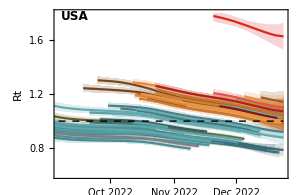
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

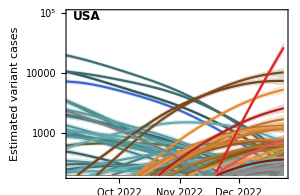
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

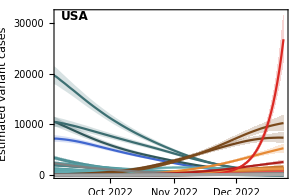
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
logitTransformDateSeries[dateSeries_]:=Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,dateSeries]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=logitTransformDateSeries[fGather[country,variant]];
lowerSeries=logitTransformDateSeries[fGatherLower[country,variant]];
upperSeries=logitTransformDateSeries[fGatherUpper[country,variant]];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{logitTransform[0.0005],logitTransform[0.9]}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

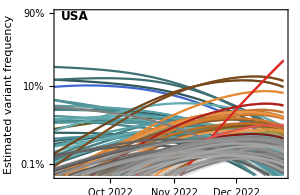
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{rtMin,rtMax},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

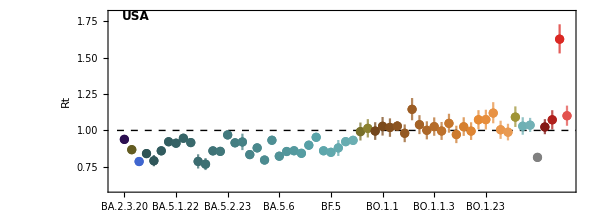

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.4},{rtMin,rtMax}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

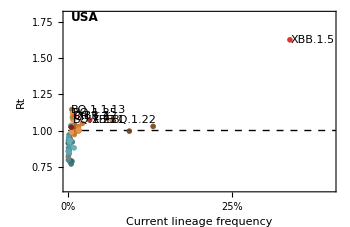
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
XBB.1.5 | 1.63 | 1.53 - 1.73
BQ.1.1.13 | 1.15 | 1.07 - 1.22
BQ.1.25 | 1.12 | 1.05 - 1.19
XBB.2 | 1.1 | 1.03 - 1.17
CH.1.1 | 1.09 | 1.02 - 1.17
BQ.1.23 | 1.07 | 1.01 - 1.14
BQ.1.22 | 1.07 | 1.01 - 1.14
XBB.1 | 1.07 | 1.01 - 1.14

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png